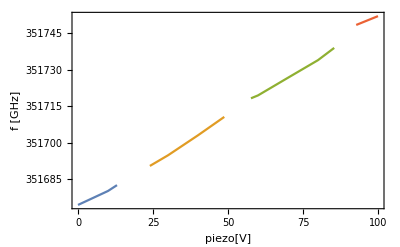

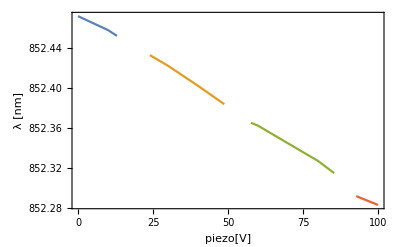

```mathematica
V={0,10,13,23.96,30,40,48.76,57.66,60,70,80,85.4,92.74,100};
f=351000+{674.46,680.2,682.6,690.5,694.87,703.1,710.66,718.31,719.5,726.77,734,739.03,748.47,752.1};
λ=299792458/f;

fdata=Thread[{V,f}];
λdata=Thread[{V,λ}];

edges={0,13,23.96,48.76,57.66,85.4,92.74,100}; (*voltages where it transitions mm to sm or vice versa; include 0 and 100.*)
fdataPart=Reap[
Do[

Sow[
Cases[fdata,x_/;x[[1]]≥ edges[[i]]&&x[[1]]≤edges[[i+1]]]
]
,{i,1,Length[edges]-1,2}]
][[2,1]];
ListPlot[fdataPart,Joined->True,Axes->False,Frame->True,FrameLabel->{"piezo[V]","f [GHz]", "F3 laser VT-0021"}]

λdataPart=Reap[
Do[

Sow[
Cases[λdata,x_/;x[[1]]≥ edges[[i]]&&x[[1]]≤edges[[i+1]]]
]
,{i,1,Length[edges]-1,2}]
][[2,1]];
ListPlot[λdataPart,Joined->True,Axes->False,Frame->True,FrameLabel->{"piezo[V]","λ [nm]", "F3 laser VT-0021"}]
```